```mathematica
Taller 10.2
```

```mathematica
Clear[f]
Clear[g]
```

ⅇ^(1-x^2)-x-x Sin[3-x]

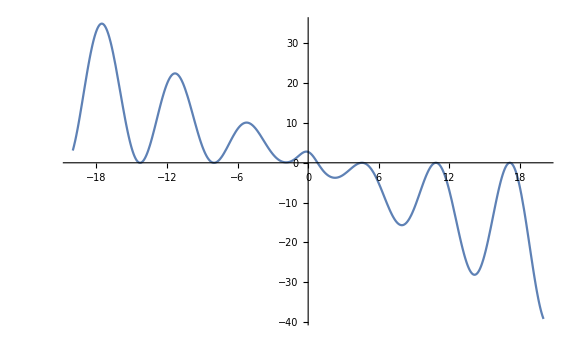

```mathematica
f[x_] := E^(-x^2+1)+x*Sin[x-3]-x
f[x]
Plot[f[x],{x,-20,20},PlotRange->Automatic,ImageSize->Large]
```

```mathematica
Biseccion
```

```mathematica
Manipulate[Plot[f[x],{x,negx,posx},PlotRange->{-5,5},ImageSize->Large],{negx, 0,-20},{posx,20,0}]
```

```mathematica
Punto Fijo
```

```mathematica
g[x_] := E^(1-x^2)+x*Sin[x-3]
g[x]
Manipulate[Plot[{f[x],g[x],x},{x,negx,posx},PlotRange->{-20,20},ImageSize->Large],{negx, 0,-20},{posx,20,0}]
Manipulate[Plot[{f[x],g'[x],1,-1},{x,negx,posx},PlotRange->{-5,5},ImageSize->Large],{negx, 0,-20},{posx,20,0}]
```

ⅇ^(1-x^2)-x Sin[3-x]

```mathematica
Newton / Secante
```

```mathematica
f'[x]
g[x_] := x-f[x]/f'[x]
Manipulate[Plot[{f[x],g[x],x},{x,negx,posx},PlotRange->{-20,20},ImageSize->Large],{negx, 0,-20},{posx,20,0}]
Manipulate[Plot[{f[x],g'[x],1,-1},{x,negx,posx},PlotRange->{-5,5},ImageSize->Large],{negx, 0,-20},{posx,20,0}]
```

-1-2 ⅇ^(1-x^2) x+x Cos[3-x]-Sin[3-x]

```mathematica
Raices multiples
```

```mathematica
f''[x]
g[x_]:= x-(f[x]*f'[x])/(f'[x]^2-f[x]*f''[x])
Manipulate[Plot[{f[x],g[x],x},{x,negx,posx},PlotRange->{-20,20},ImageSize->Large],{negx, 0,-20},{posx,20,0}]
Manipulate[Plot[{f[x],g'[x],1,-1},{x,negx,posx},PlotRange->{-5,5},ImageSize->Large],{negx, 0,-20},{posx,20,0}]
```

-2 ⅇ^(1-x^2)+4 ⅇ^(1-x^2) x^2+2 Cos[3-x]+x Sin[3-x]